```mathematica
ClearAll["Global`*"]
```

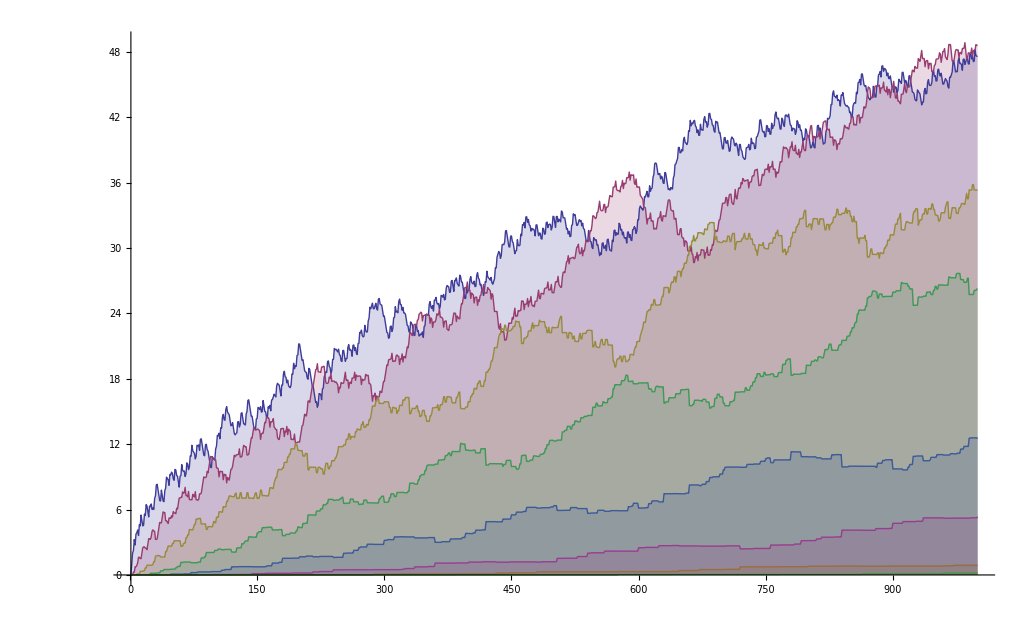

```mathematica
d2[n_,k_]:=d2[n,k]=Sum[d2[j,k-1] d2[n/j,1],{j,Divisors[n]}];d2[n_,1]:=1;d2[1,1]:=0;d2[n_,0]:=0;d2[1,0]:=1
D2[n_,k_]:=D2[n,k]=Sum[d2[j,k],{j,2,n}]
d[n_,z_]:=d[n,z]=Product[1/(p[[2]]!) Pochhammer[z,p[[2]]],{p,FI[n]}];FI[n_]:=If[n==1,{},FactorInteger[n]]
DD[n_,k_]:=DD[n,k]=Sum[d[j,k],{j,1,n}]
Li[n_,a_,k_]:= Re[Li[n,a,k]=(-1)^(k+1)/k Sum[(-1)^(k-j) Binomial[k,j] DD[n,a j],{j,0,k}]/a]
Li2[n_,a_] := Sum[ Li[n,a,k],{k,1,Log[2,n]}]

DiscretePlot[{ Li[n,ss=-.5,1], Li[n,ss,2], Li[n,ss,3], Li[n,ss,4], Li[n,ss,5], Li[n,ss,6], Li[n,ss,7], Li[n,ss,8]},{n,1,1000}]
```

```mathematica
Li2[100,-I]
```

428/15

```mathematica
Li[100,I,1]
```

65/8+(2953 ⅈ)/72

```mathematica
Li[100,1,1]
```

99

```mathematica
Li[100,-1,1]
```

0

```mathematica
Li[100,-I,1]
```

65/8-(2953 ⅈ)/72

```mathematica
Table[{n,d[n,-1/2]},{n,1,100}] // TableForm
```

1 | 1
2 | -1/2
3 | -1/2
4 | -1/8
5 | -1/2
6 | 1/4
7 | -1/2
8 | -1/16
9 | -1/8
10 | 1/4
11 | -1/2
12 | 1/16
13 | -1/2
14 | 1/4
15 | 1/4
16 | -5/128
17 | -1/2
18 | 1/16
19 | -1/2
20 | 1/16
21 | 1/4
22 | 1/4
23 | -1/2
24 | 1/32
25 | -1/8
26 | 1/4
27 | -1/16
28 | 1/16
29 | -1/2
30 | -1/8
31 | -1/2
32 | -7/256
33 | 1/4
34 | 1/4
35 | 1/4
36 | 1/64
37 | -1/2
38 | 1/4
39 | 1/4
40 | 1/32
41 | -1/2
42 | -1/8
43 | -1/2
44 | 1/16
45 | 1/16
46 | 1/4
47 | -1/2
48 | 5/256
49 | -1/8
50 | 1/16
51 | 1/4
52 | 1/16
53 | -1/2
54 | 1/32
55 | 1/4
56 | 1/32
57 | 1/4
58 | 1/4
59 | -1/2
60 | -1/32
61 | -1/2
62 | 1/4
63 | 1/16
64 | -21/1024
65 | 1/4
66 | -1/8
67 | -1/2
68 | 1/16
69 | 1/4
70 | -1/8
71 | -1/2
72 | 1/128
73 | -1/2
74 | 1/4
75 | 1/16
76 | 1/16
77 | 1/4
78 | -1/8
79 | -1/2
80 | 5/256
81 | -5/128
82 | 1/4
83 | -1/2
84 | -1/32
85 | 1/4
86 | 1/4
87 | 1/4
88 | 1/32
89 | -1/2
90 | -1/32
91 | 1/4
92 | 1/16
93 | 1/4
94 | 1/4
95 | 1/4
96 | 7/512
97 | -1/2
98 | 1/16
99 | 1/16
100 | 1/64

```mathematica
Li[1000,1/2,2]
```

-4431721/8192

```mathematica
Animate[DiscretePlot[{  Li[n,ss,1]},{n,1,100}],{ss,-2,2}]
```

```mathematica
Lia[n_,a_,k_]:= Re[Lia[n,a,k]=Sum[(-1)^(k-j) Binomial[k,j] DD[n,a j],{j,0,k}]]
```

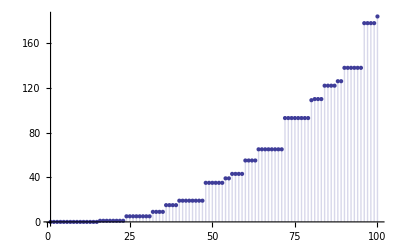

```mathematica
DiscretePlot[Lia[n,1,4],{n,1,100}]
```

```mathematica
Sum[ d[j,1/2] DD[Floor[1000/j],1/2],{j,1,1000}]
```

1000

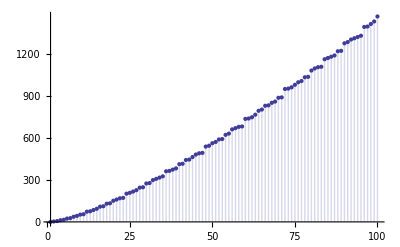

```mathematica
DiscretePlot[Re[Lia[n,3 ,1]],{n,1,100}]
```

```mathematica
Series[(x^3+1)^3,{x,0,20}]
```

1+3 x^3+3 x^6+x^9+O[x]^21

```mathematica
DX[n_,z_]:=Sum[FactorialPower[z,a]/a! Da[n,a],{a,0,Log[2,n]}]
Lia2[n_,a_,k_]:= Lia[n,a,k]=Sum[(-1)^(k-j) Binomial[k,j] DX[n,a j],{j,0,k}]
Table[ {a, Expand[Lia2[10000,ss=2,a]]},{a,1,16}] // TableForm
```

1 | 2 Da[10000,1]+Da[10000,2]
2 | 4 Da[10000,2]+4 Da[10000,3]+Da[10000,4]
3 | 8 Da[10000,3]+12 Da[10000,4]+6 Da[10000,5]+Da[10000,6]
4 | 16 Da[10000,4]+32 Da[10000,5]+24 Da[10000,6]+8 Da[10000,7]+Da[10000,8]
5 | 32 Da[10000,5]+80 Da[10000,6]+80 Da[10000,7]+40 Da[10000,8]+10 Da[10000,9]+Da[10000,10]
6 | 64 Da[10000,6]+192 Da[10000,7]+240 Da[10000,8]+160 Da[10000,9]+60 Da[10000,10]+12 Da[10000,11]+Da[10000,12]
7 | 128 Da[10000,7]+448 Da[10000,8]+672 Da[10000,9]+560 Da[10000,10]+280 Da[10000,11]+84 Da[10000,12]+14 Da[10000,13]
8 | 256 Da[10000,8]+1024 Da[10000,9]+1792 Da[10000,10]+1792 Da[10000,11]+1120 Da[10000,12]+448 Da[10000,13]
9 | 512 Da[10000,9]+2304 Da[10000,10]+4608 Da[10000,11]+5376 Da[10000,12]+4032 Da[10000,13]
10 | 1024 Da[10000,10]+5120 Da[10000,11]+11520 Da[10000,12]+15360 Da[10000,13]
11 | 2048 Da[10000,11]+11264 Da[10000,12]+28160 Da[10000,13]
12 | 4096 Da[10000,12]+24576 Da[10000,13]
13 | 8192 Da[10000,13]
14 | 0
15 | 0
16 | 0

```mathematica
Expand[Liax[10000,2,3]]
```

8 x^3+12 x^4+6 x^5+x^6

```mathematica
DX[n_,z_]:=Sum[FactorialPower[z,a]/a! Da[n,a],{a,0,Log[2,n]}]
Lia2[n_,a_,k_]:= Lia[n,a,k]=Sum[(-1)^(k-j) Binomial[k,j] DX[n,a j],{j,0,k}]
Sum[ Expand[(-1)^(a+1)/a Lia2[10000,ss=4,a]/ss],{a,1,16}]
```

Da[10000,1]-1/2 Da[10000,2]+1/3 Da[10000,3]-1/4 Da[10000,4]+1/5 Da[10000,5]-1/6 Da[10000,6]+1/7 Da[10000,7]-1/8 Da[10000,8]+1/9 Da[10000,9]-1/10 Da[10000,10]+1/11 Da[10000,11]-1/12 Da[10000,12]+1/13 Da[10000,13]

```mathematica
Liax
```

Liax

```mathematica
Liay[n_,a_,k_]:= Expand[Sum[(-1)^(k-j) Binomial[k,j](x+1)^(a j),{j,0,k}]]
```

```mathematica
Liay[10000,2,6]
```

64 x^6+192 x^7+240 x^8+160 x^9+60 x^10+12 x^11+x^12

```mathematica
d
```

```mathematica
Series[Log[x^2],{x,0,30}]
```

2 Log[x]+O[x]^31

```mathematica
Sum[ Expand[(-1)^(a) Lia2[10000,ss=3,a]],{a,1,16}]
```

-3 Da[10000,1]+6 Da[10000,2]-10 Da[10000,3]+15 Da[10000,4]-21 Da[10000,5]+28 Da[10000,6]-36 Da[10000,7]+45 Da[10000,8]-55 Da[10000,9]+66 Da[10000,10]-78 Da[10000,11]+91 Da[10000,12]-105 Da[10000,13]